Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

{0.0043425,4.75}

{{0,123.1,2.2},{2,126.2,1.4},{4,126.2,1.4},{6,126.3,1.3},{8,126.303,1.35991},{10,126.3,1.3}}

{{0,123.1,2.2},{2,126.2,1.4},{4,126.2,1.4},{6,126.3,1.3},{8,126.3,1.4},{10,126.3,1.3}}

{125.733}

{4.73493+0.000028022 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.000028022 | 0.000261484 | 0.107165 | 0.916588
b | 4.73493 | 0.030466 | 155.417 | 9.80759×10^-20}

{-2.68701+0.0966769 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0966769 | 0.00289138 | 33.4362 | 6.98765×10^-10
b | -2.68701 | 0.157375 | -17.074 | 1.40669×10^-7}

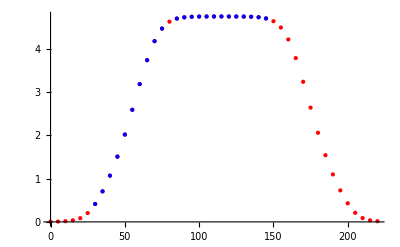

```mathematica
Clear[Sub, Filename, Filepath, rawData, partitionedData, gradientData, UnitsToMM, ArrayUnitsToMM, current, Lv, Lvc];
current = 8;
Filename = "m3-quad-"<>ToString[current]<>"A"; 
Filepath = StringJoin[NotebookDirectory[], "../data/"]; 

rawData = Import[StringJoin[Filepath, Filename, ".txt"], "Table"]; 

partitionedData = Partition[SortBy[Drop[rawData, 2], #1[[1]] + 100*#1[[2]] & ], 45]; 

Sub[n_] := partitionedData[[n]] - partitionedData[[n + 1]]; 

ArrayUnitsToMM[a_, b_] := (UnitsToMM[#1, b] & ) /@ a; 
UnitsToMM[a_, b_] := {b*(a[[1]] - 1), a[[2]]}; 

gradientData = ReplacePart[(Sub[#1] & ) /@ Range[5], {i_, j_, 1} -> j][[All,All,{1, 3}]]; 
gradientData = (ArrayUnitsToMM[#1, 5] & ) /@ gradientData; 

xGradientData = (gradientData[[All,#1]] & ) /@ Range[45];
xGradientDataT = Transpose[xGradientData];
Subscript[g, max]= Map[Last,Flatten[Take[xGradientData, {18,30}],1]];
Subscript[g, max]={Mean[Subscript[g, max]], StandardDeviation[Subscript[g, max]]};

gV = Map[Integrate[Interpolation[#, InterpolationOrder -> 1][x], {x, 0, 220}]&,xGradientDataT];
gV = {Mean[gV], StandardDeviation[gV]};

Lvc={current, gV[[1]]/Subscript[g, max][[1]], Sqrt[(gV[[2]]/Subscript[g, max][[1]])^2+(Subscript[g, max][[2]]*gV[[1]]/Subscript[g, max][[1]]^2)^2]};

xGradientData = ({#1[[1]][[1]], (1/8)*Mean[#1[[All,2]]], (1/8)*StandardDeviation[#1[[All,2]]]} & ) /@ xGradientData; 
{Min[xGradientData[[All,2]]], Max[xGradientData[[All,2]]]}


path = StringJoin[Filepath, "parsed/", "m3-quad", "-MagneticLengths", ".txt"];
Lv = Import[path, "Table"];
Lv = ReplacePart[Lv, current/2+1 -> Lvc];
Lv = Map[{#[[1]], Round[#[[2]], 0.1], Round[#[[3]], 0.1]}&,Lv]
{Mean[Lv[[All,2]]]}
Export[path, Lv, "Table"];


path = StringJoin[Filepath, "parsed/", Filename, "-MeanGradients", ".txt"]; 
Export[path, xGradientData, "Table"]; 


xOnlyGradient = ({#1[[1]], #1[[2]]} & ) /@ xGradientData; 

GradientPlateau = Take[xOnlyGradient, {18, 30}]; 
GradientEdge = Take[xOnlyGradient, {7, 16}]; 

nlmPlateau = NonlinearModelFit[GradientPlateau, a*x + b, {a, b}, x]; 
nlmEdge = NonlinearModelFit[GradientEdge, a*x + b, {a, b}, x]; 
nlmPlateau[{"BestFit", "ParameterTable"}]
nlmEdge[{"BestFit", "ParameterTable"}]

Show[ListPlot[xOnlyGradient, PlotStyle -> Red], ListPlot[GradientEdge, PlotStyle -> Blue], ListPlot[GradientPlateau, PlotStyle -> Blue]]
```